```mathematica
n=50;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,16}]];
AdjacencyGraph[k]*)
```

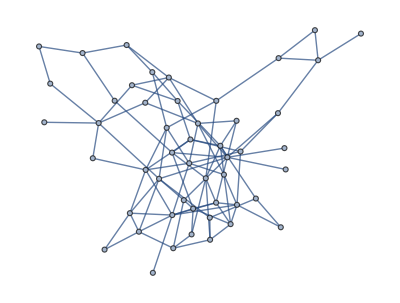
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<200>, {50, 50}]

```mathematica
data={-0.8294007492406162,-0.668120055620453,0.8567281556108657,-0.3745859168862727,0.7895286473042089,0.1717990034361509,-0.062474380661977295,-0.49899403280264754,-0.3923690733979398,-0.4371373249931661,0.3251931812020732,0.05411859848357265,0.824215257790465,-0.14313918638036874,0.46849876671505997,0.7609244170038704,-0.1147397960676638,0.10970537640134859,0.6151379059473552,0.9345828535458041,-0.8978791683752146,0.9099542910854896,-0.2733845963887199,-0.2635580153443352,0.13503173455572204,0.23944197204420284,0.438271058593663,-0.23345182003349493,-0.06050612751928598,0.42198146431729816,0.20074177723396816,-0.2690684409271857,-0.3627263118734953,-0.7014164512721399,-0.4529200913505159,-0.12387158345716567,0.3112981545930536,-0.9959128773235539,-0.06371155704724163,-0.2562377053852675,-0.1786861144958326,0.1859654004304861,0.3318577631014024,-0.5560838994499658,0.04602237718698198,-0.02382903627555023,-0.10515134939367732,-0.32345149473744217,0.3529200495473485,-0.4623989417288074};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,5],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==6-4/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}];
Print[ukupfrust[5000]];
data2a=Flatten[Table[Mod[Subscript[z,i][5000],2Pi],{i,1,n}]]
```

{0.}

{2.39547,2.39547,0.824677,3.96627,5.53707,3.96627,2.39547,3.96627,2.39547,0.824677,3.96627,3.96627,5.53707,5.53707,5.53707,5.53707,2.39547,5.53707,5.53707,3.96627,0.824677,0.824677,5.53707,3.96627,3.96627,0.824677,3.96627,3.96627,2.39547,5.53707,2.39547,3.96627,3.96627,2.39547,0.824677,2.39547,3.96627,2.39547,3.96627,3.96627,3.96627,5.53707,3.96627,3.96627,5.53707,3.96627,5.53707,2.39547,5.53707,5.53707}

```mathematica
m=3;
k2=k;
k2[[2]][[1]]=1;
k2[[1]][[2]]=1;
k2[[4]][[6]]=1;
k2[[6]][[4]]=1;
k2[[49]][[50]]=1;
k2[[50]][[49]]=1;
k2[[13]][[14]]=1;
k2[[14]][[13]]=1;
dataa=Flatten[Table[Subscript[z,i][30],{i,1,n}]];
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns1=Table[{Subscript[∅1,i]'[t]==6-3/n Sum[k2[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅1,j][t]-Subscript[∅1,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅1,i][0]==dataa[[i]]},{i,1,n}];
vars1=Table[Subscript[∅1,i][t],{i,1,n}];
sol1=NDSolve[eqns1,vars1,{t,0,10000}];
Do[Subscript[z1,i][t_]:=Evaluate[Subscript[∅1,i][t]/.sol1],{i,1,n}];
Do[Subscript[zz1,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅1,i][t]/.sol1)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz1,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z1,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z1,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k2];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}];
ukupfrust1[t_]:=Sum[k2[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z1,j][t]-Subscript[z1,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}];
Print[ukupfrust1[5000]];
data2b=Flatten[Table[Mod[Subscript[z1,i][tt],2Pi],{i,1,n}]]
```

{0.}

{2.77989,4.35069,2.77989,5.92149,1.2091,4.35069,4.35069,5.92149,4.35069,2.77989,5.92149,5.92149,1.2091,5.92149,1.2091,1.2091,4.35069,1.2091,1.2091,5.92149,2.77989,2.77989,1.2091,4.35069,5.92149,2.77989,5.92149,5.92149,4.35069,1.2091,4.35069,5.92149,5.92149,4.35069,2.77989,4.35069,5.92149,4.35069,5.92149,5.92149,5.92149,1.2091,5.92149,5.92149,1.2091,5.92149,1.2091,4.35069,2.77989,1.2091}

```mathematica
zvuk1={2,2,1,3,4,3,2,3,2,1,3,3,4,4,4,4,2,4,4,3,1,1,4,3,3,1,3,3,2,4,2,3,3,2,1,2,3,2,3,3,3,4,3,3,4,3,4,2,4,4};
```

```mathematica
zvuk2={2,3,2,4,1,3,3,4,3,2,4,4,1,4,1,1,3,1,1,4,2,2,1,3,4,2,4,4,3,1,3,4,4,3,2,3,4,3,4,4,4,1,4,4,1,4,1,3,2,1};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a1=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,30}],{i,1,n}];
```

```mathematica
a2=30+Table[findAllRoots[Sin[(Subscript[z1,i][t])/2],{t,0,30}],{i,1,n}];
```

```mathematica
a=Table[Join[a1[[i]],a2[[i]]],{i,1,n}];
```

```mathematica
Sound[Flatten[{Table[Table[If[Round[a1[[i]][[j]],0.1]==t,If[zvuk1[[i]]==1,SoundNote["G",{t,t+0.1},"Marimba"],If[zvuk1[[i]]==2,SoundNote["B",{t,t+0.1},"Marimba"],If[zvuk1[[i]]==3,SoundNote["D",{t,t+0.1},"Marimba"],SoundNote["F",{t,t+0.1},"Marimba"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a1[[i]]]}],{t,0,29.9,0.1}],Table[Table[If[Round[a2[[i]][[j]],0.1]==t,If[zvuk2[[i]]==1,SoundNote["G",{t,t+0.1},"Marimba"],If[zvuk2[[i]]==2,SoundNote["B",{t,t+0.1},"Marimba"],If[zvuk2[[i]]==3,SoundNote["D",{t,t+0.1},"Marimba"],SoundNote["F",{t,t+0.1},"Marimba"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a2[[i]]]}],{t,30,60,0.1}]}],{0,80.133}]
```

```mathematica
Export["sim11_marimba.mp3",%53]
```

sim11_marimba.mp3

```mathematica
Export["MIDI_SM11.mid",%53]
```

MIDI_SM11.mid

```mathematica
granica=60;
```

```mathematica
video[t_]:=Grid[{{AdjacencyGraph[k2,EdgeStyle->If[t≤30,{1<->2->White,4<->6->White,49<->50->White,13<->14->White},{1<->2->Directive[Red,Thickness[0.0035]],4<->6->Directive[Red,Thickness[0.0035]],49<->50->Directive[Red,Thickness[0.0035]],13<->14->Directive[Red,Thickness[0.0035]]}],VertexStyle->Table[i->If[MemberQ[Round[a[[i]],0.1],t],White,Black],{i,1,n}],VertexSize->0.6,ImageSize->700],Show[{Plot[If[tt≤30,ukupfrust[tt],ukupfrust1[tt-30]],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

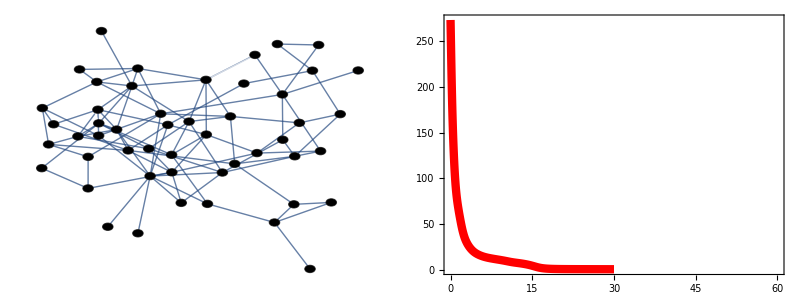

```mathematica
video[30.]
```

```mathematica
simulaci2=Flatten[Table[Table[video[t],{i,1,2}],{t,0,60,0.1}]];
```

```mathematica
Export["SM11.AVI",simulaci2]
```